```mathematica
(*
  yE - Enzyme concentration
yI - Inhibitor compound concentration
yEI1 -  Enzyme-inhibitor complex 
yEI2 -  Inactivated enzyme (covalently bonded inhibitor)

yS - Substrate concentration
yES - Substrate-enzyme complex
yP - Product concentration

  k1S, k1Srev - Forward and reverse substrate binding rates
  k1, k1rev - Forward and reverse inhibitor binding rates
  kcatS - Catalytic rate of product formation
  kinac - Inhibitor inactivation rate
*)
```

```mathematica
EnzymeInhibitorODE[k1S_,k1Srev_,k1_,k1rev_,kcatS_,kinact_]:={
yE'[t]==(k1Srev+kcatS) yES[t]+ k1rev yEI1[t]-k1 yE[t] yI[t] -k1S yE[t] yS[t],
yI'[t] ==k1rev yEI1[t]-k1 yE[t] yI[t],
yS'[t]== k1Srev yES[t] -k1S yE[t] yS[t],
yP'[t]==kcatS yES[t],
yEI1'[t] ==k1 yE[t] yI[t] - (kinact+k1rev)yEI1[t],
yEI2'[t] ==kinact yEI1[t] ,
yES'[t] == k1S yE[t] yS[t]-(kcatS + k1Srev)yES[t]
};
```

```mathematica
EnzymeInhibitor3ODE[k1S_,k1Srev_,k1_,k1rev_,k2_,k2rev_,kinact_,kcatS_]:={
yE'[t]==(k1Srev+kcatS) yES[t]+ k1rev yEI1[t]-k1 yE[t] yI[t] -k1S yE[t] yS[t],
yI'[t] ==k1rev yEI1[t]-k1 yE[t] yI[t],
yS'[t]== k1Srev yES[t] -k1S yE[t] yS[t],
yP'[t]==kcatS yES[t],
yEI1'[t] ==k1 yE[t] yI[t] - (k2+k1rev)yEI1[t]+k2rev yEI2[t],
yEI2'[t] ==k2 yEI1[t] -(k2rev+kinact)yEI2[t],
yEI3'[t]== kinact yEI2[t],
yES'[t] == k1S yE[t] yS[t]-(kcatS + k1Srev)yES[t]
};
```

```mathematica
kt=300*1.987*10^(-3)(* kcal/mol *)
```

0.5961

```mathematica
hNa=6.022*10^23 * 6.626*10^(-34)/4184 (*J s * mol^1 * kcal/J*)
```

9.53675×10^-14

```mathematica
arrh=kt/hNa
```

6.25056×10^12

```mathematica
dGBarToRate[dGBar_]:=arrh*Exp[-dGBar/kt]
```

## ATP Parameters

```mathematica
(* Parameters for ATP*)
KmATP=150; (* μM - Liclican (2020) *)
keffATP = 3.7*10^-3;(* 1/( s μM) - Dinh (2006) catalytic efficiency of activated wild type BTK *)
```

```mathematica
ksATP=keffATP*KmATP  (* 1 / s  Estimate for the rate of product formation *)
```

0.555

```mathematica
k1ATP = 0.05; (* (1 / (s nM) Estimate for k1 binding rate for ATP*)
k1revATP=k1ATP*KmATP*1000-ksATP
```

7499.45

## BTK (Liclican Fig. 3)

```mathematica
Ki=60; (* Estimate of Liclican experiment*)
keff=3.0*10^-5 ; (* 1/(nM s), Liclican (2020) Table 3 BTK-Acalabrutinib *)
kinac=keff*Ki
```

0.0018

```mathematica
k1btk=0.1;  (* 1/( s nM), estimate*)
k1revbtk = k1btk*Ki
```

6.

```mathematica
(*  Approximate reproduction of Liclican (2020) Figure 3
  Initial enzyme concentration: 5 nM
ATP concentration: 300 μM
Inhibitor compound concentration range: 0 - 160 nm
*)
```

```mathematica
i0tbl={0,0.1,0.25,1.0,2.5,5,10,20,40,80,160};
```

```mathematica
solFig3=Table[NDSolve[
Join[
EnzymeInhibitorODE[k1ATP, k1revATP, k1btk,k1revbtk,ksATP,kinac],
{yE[0]==5,yI[0]==i0,yS[0]==300000,
yP[0]==0,yEI1[0]==0,yEI2[0]==0,yES[0]==0}
],{yE,yI, yS,yP,yEI1,yEI2,yES},{t,0,40000}
],{i0,i0tbl}];
```

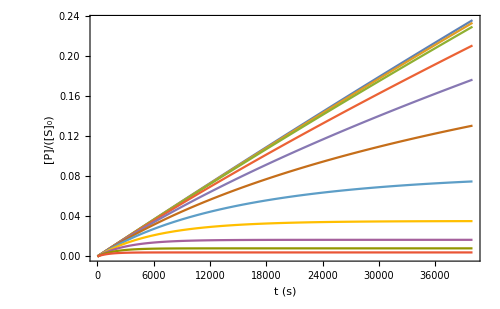

```mathematica
Plot[Evaluate@Table[yP[t]/yS[0]/.s,{s,solFig3}],{t,0,40000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},
Frame->True,FrameLabel->{"t (s)", "[P]/([S]_0)"},RotateLabel->False
]
```

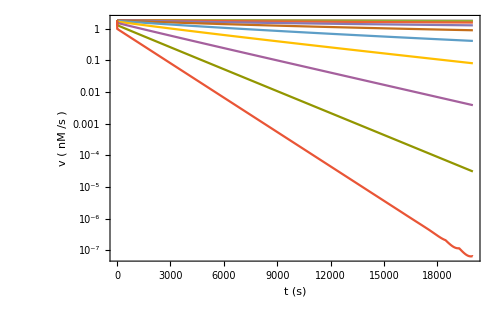

```mathematica
Plot[Evaluate@Table[yP'[t]/.s,{s,solFig3}],{t,0,20000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},ScalingFunctions->{None,"Log"},
Frame->True,FrameLabel->{"t (s)", "v ( nM /s )"},RotateLabel->False
]
```

```mathematica
kobs=Transpose@{i0tbl,Table[-(Log[yP'[15000]]-Log[yP'[10000]])/5000/.s[[1]],{s,solFig3}]};
```

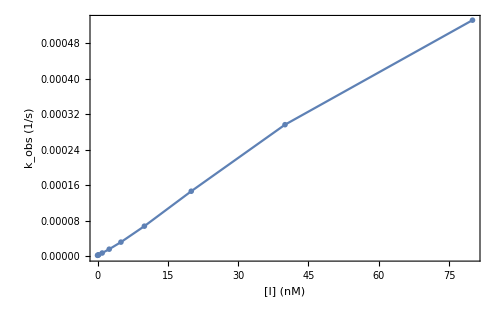

```mathematica
ListLinePlot[kobs[[;;-2]],
ImageSize->500,LabelStyle->{14,Black},PlotMarkers->"OpenMarkers",
PlotRange->Automatic,
Frame->True,FrameLabel->{"[I] (nM)", "k_obs (1/s)"},RotateLabel->False
]
```

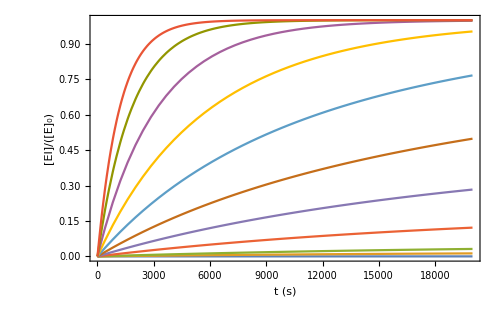

```mathematica
Plot[Evaluate@Table[yEI2[t]/yE[0]/.s,{s,solFig3}],{t,0,20000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},
Frame->True,FrameLabel->{"t (s)", "[EI]/([E]_0)"},RotateLabel->False
]
```

```mathematica
ttbl={10,100,1000,2000,4000,10000,14000,20000,30000,40000}
```

{10,100,1000,2000,4000,10000,14000,20000,30000,40000}

```mathematica
ic50tbl=Transpose@{N@i0tbl[[2;;]],#}&/@Table[yEI2[t]/yE[0]/.s[[1]],{t,ttbl},{s,solFig3[[2;;]]}];
```

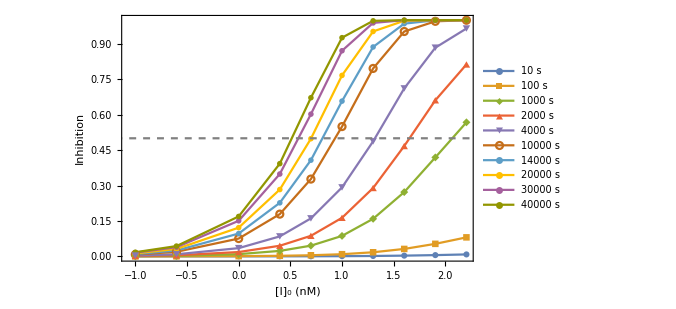

```mathematica
Show[ListLinePlot[ic50tbl,PlotMarkers->Automatic,
Frame->True,FrameLabel->{"[I]_0 (nM)", "Inhibition"},
ImageSize->500,LabelStyle->{14,Black},
ScalingFunctions->{"Log10",None},
PlotLegends->(ToString[NumberForm[#]]<>" s"&)/@ttbl
],
Plot[0.5,{x,0.01,1000},ScalingFunctions->{"Log10",None},PlotStyle->{{Gray,Dashed}}]
]
```

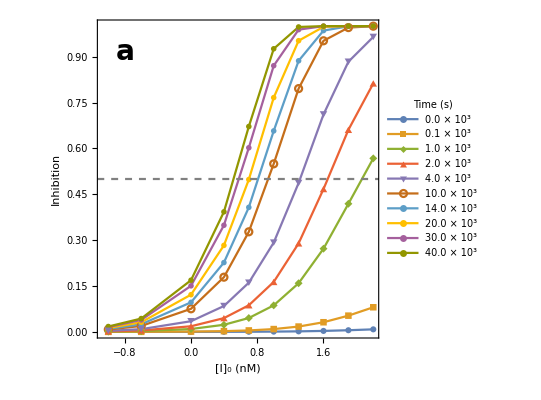

```mathematica
ic50BTKplt=Show[ListLinePlot[ic50tbl,PlotMarkers->Automatic,PlotRange->All,
Frame->True,FrameLabel->{"[I]_0 (nM)", "Inhibition"},FrameStyle->Directive[Black],
ImageSize->400,AspectRatio->1,LabelStyle->{16,Black},
ScalingFunctions->{"Log10",None},
Epilog->{Inset[Style["a",28,Bold],Scaled@{0.1,0.9}]},
PlotLegends->Placed[LineLegend[(ToString[NumberForm[#/1000//N,{3,1}]]<>" × 10^3"&)/@ttbl, LegendLabel->"Time (s)"],Right]],
Plot[0.5,{x,0.05,1000},
ScalingFunctions->{"Log10",None},
PlotStyle->{{Gray,Dashed}}]
]
```

```mathematica
Export["ic50_btk_assay.pdf",ic50BTKplt]
```

ic50_btk_assay.pdf

## BTK (Liclican Fig. 3)

## BTK EVB

```mathematica
Kmat={{0.06420530806846016,4.70634714736842},{1.4593234252643285*^7,2.3442817466622215*^-29}}
```

{{0.0642053,4.70635},{1.45932×10^7,2.34428×10^-29}}

```mathematica
k1rev=dGBarToRate[12] (* 1/s, 12 kcal/mol dissociation barrier*)
```

11303.2

```mathematica
Ki6j6m=Exp[-6.79/kt]*10^(9) (* nM, PDLD 3.2 kcal/mol binding energy*)
k1=k1rev/Ki6j6m (* 1 / (s nM) *)
```

11300.

1.00028

```mathematica
(* 
  Inhibitor concentration: 1 μM - 32 μM
 *)
```

```mathematica
i0tblevb={0,100,200,500,1000,2000, 4000,8000,16000,32000}
```

{0,100,200,500,1000,2000,4000,8000,16000,32000}

```mathematica
sol6j6m=Table[NDSolve[
Join[
EnzymeInhibitor3ODE[k1ATP, k1revATP, k1,k1rev,Kmat[[1,1]],Kmat[[1,2]],Kmat[[2,1]], ksATP],
{yE[0]==5,yI[0]==i0,yS[0]==300000,
yP[0]==0,yEI1[0]==0,yEI2[0]==0,yEI3[0]==0,yES[0]==0}
],{yE,yI, yS,yP,yEI1,yEI2,yEI3,yES},{t,0,40000}
],{i0,i0tbl}];
```

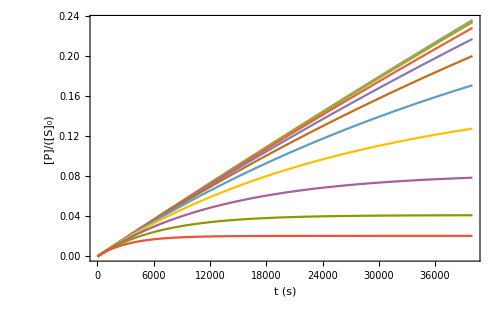

```mathematica
Plot[Evaluate@Table[yP[t]/yS[0]/.s,{s,sol6j6m}],{t,0,40000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},
Frame->True,FrameLabel->{"t (s)", "[P]/([S]_0)"},RotateLabel->False
]
```

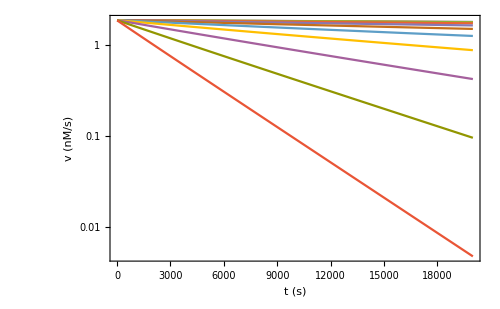

```mathematica
Plot[Evaluate@Table[yP'[t]/.s,{s,sol6j6m}],{t,0,20000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},ScalingFunctions->{None,"Log"},
Frame->True,FrameLabel->{"t (s)", "v (nM/s)"},RotateLabel->False
]
```

```mathematica
kobs6j6m=Transpose@{i0tbl,Table[-(Log[yP'[15000]]-Log[yP'[10000]])/5000/.s[[1]],{s,sol6j6m}]};
```

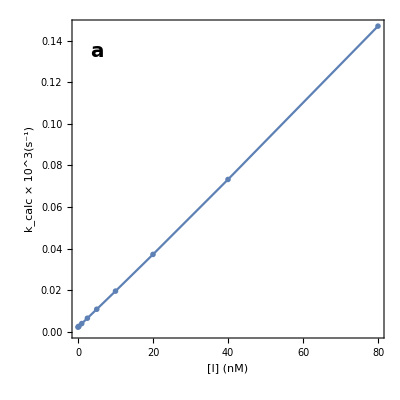

```mathematica
kobsplt6j6m=ListLinePlot[{#1,#2*1000}&@@@kobs6j6m[[;;-2]],
ImageSize->400,AspectRatio->1,LabelStyle->{16,Black},PlotMarkers->"OpenMarkers",
PlotRange->Automatic, Frame->True,FrameStyle->Directive[Black],FrameLabel->{"[I] (nM)", "k_calc × 10^3(s^-1)"},RotateLabel->False,
Epilog->{Inset[Style["a",20,Bold],Scaled@{0.08,0.9}]}
]
```

```mathematica
Export["kcalc_6j6m.pdf",kobsplt6j6m]
```

kcalc_6j6m.pdf

```mathematica
kobs6j6m[[;;-2]]
```

{{0,2.28127×10^-6},{0.1,2.45243×10^-6},{0.25,2.70924×10^-6},{1.,3.99475×10^-6},{2.5,6.57273×10^-6},{5,0.0000108893},{10,0.000019592},{20,0.0000372384},{40,0.0000732562},{80,0.000146948}}

```mathematica
kobsLm6j6m=LinearModelFit[kobs6j6m,x,x]
```

FittedModel[1.57192×10^-6+1.835×10^-6 x]

```mathematica
u1ATP=1+300/KmATP
```

3

```mathematica
kobsLm6j6m["ParameterTableEntries"][[2,1]]*u1ATP (*observed kinac/Ki *)
```

5.50499×10^-6

```mathematica
Kmat[[1,1]]/Ki6j6m
```

5.68188×10^-6

```mathematica
ttbl={100,1000,2000,4000,10000,14000,20000,30000,40000}
```

{100,1000,2000,4000,10000,14000,20000,30000,40000}

```mathematica
ic50tbl6j6m=Transpose@{N@i0tbl[[2;;]],#}&/@Table[yEI3[t]/yE[0]/.s[[1]],{t,ttbl},{s,sol6j6m[[2;;]]}];
```

```mathematica
ic50tbl6j6m[[-1]]
```

{{0.1,0.00674042},{0.25,0.016773},{1.,0.0655553},{2.5,0.156495},{5.,0.290011},{10.,0.499691},{20.,0.755532},{40.,0.94372},{80.,0.997165},{160.,0.999993}}

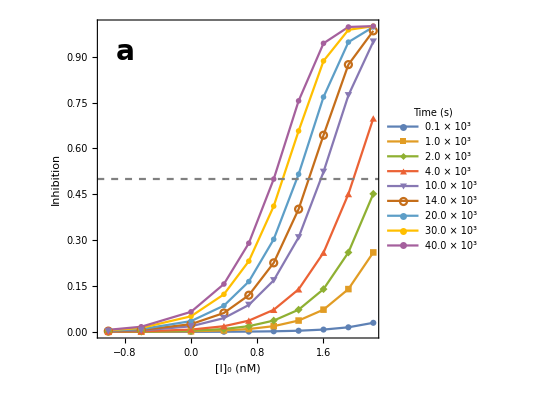

```mathematica
ic506j6mplt=Show[ListLinePlot[ic50tbl6j6m,PlotMarkers->Automatic,PlotRange->All,
Frame->True,FrameLabel->{"[I]_0 (nM)", "Inhibition"},FrameStyle->Directive[Black],
ImageSize->400,AspectRatio->1,LabelStyle->{16,Black},
ScalingFunctions->{"Log10",None},
Epilog->{Inset[Style["a",28,Bold],Scaled@{0.1,0.9}]},
PlotLegends->Placed[LineLegend[(ToString[NumberForm[#/1000//N,{3,1}]]<>" × 10^3"&)/@ttbl, LegendLabel->"Time (s)"],Right]],
Plot[0.5,{x,0.05,1000},
ScalingFunctions->{"Log10",None},
PlotStyle->{{Gray,Dashed}}]
]
```

```mathematica
Export["ic50_6j6m.pdf",ic506j6mplt]
```

ic50_6j6m.pdf

## BTK EVB

## ITK (Liclican)

```mathematica
(* Parameters for ATP*)
(* KmATPitk=50; (* μM - Liclican (2020) *)*)
```

```mathematica
KmATPitk=36;(* μM - Marcy (2001) *)
```

```mathematica
ksATPitk=0.63/60(* 1/s Marcy (2001)*)
```

0.0105

```mathematica
k1ATPitk= 0.1; (* (1 / (s nM) Estimate for k1 binding rate for ATP*)
```

```mathematica
k1revATPitk=k1ATPitk*KmATPitk*1000-ksATPitk
```

3599.99

```mathematica
Kiitk=10000; (* Estimate of Liclican experiment*)
keffitk=7.*10^-9; (* 1/(nM s), Liclican (2020) Table 3 BTK-Acalabrutinib *)
kinacitk=keffitk*Kiitk
```

0.00007

```mathematica
k1itk=0.1;  (* 1/( s nM), estimate*)
k1revitk = k1itk*Kiitk
```

1000.

```mathematica
(*  
  Initial enzyme concentration: 5 nM
ATP concentration: 100 μM
Inhibitor compound concentration range: 0 - 2560 nm
*)
```

```mathematica
i0tblitk={0,40,80,160,320,640,1280,2560};
```

```mathematica
solExpItk=Table[NDSolve[
Join[
EnzymeInhibitorODE[k1ATPitk, k1revATPitk, k1itk,k1revitk,ksATPitk,kinacitk],
{yE[0]==5,yI[0]==i0,yS[0]==100000,
yP[0]==0,yEI1[0]==0,yEI2[0]==0,yES[0]==0}
],{yE,yI, yS,yP,yEI1,yEI2,yES},{t,0,300000}
],{i0,i0tblitk}];
```

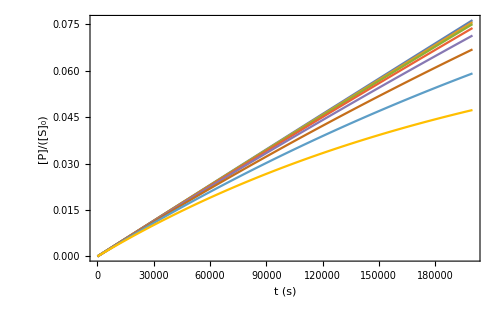

```mathematica
Plot[Evaluate@Table[yP[t]/yS[0]/.s,{s,solExpItk}],{t,0,200000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},
Frame->True,FrameLabel->{"t (s)", "[P]/([S]_0)"},RotateLabel->False
]
```

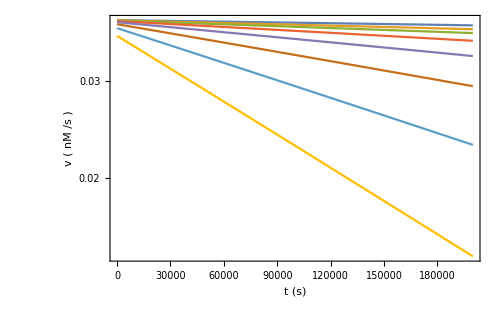

```mathematica
Plot[Evaluate@Table[yP'[t]/.s,{s,solExpItk}],{t,0,200000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},ScalingFunctions->{None,"Log"},
Frame->True,FrameLabel->{"t (s)", "v ( nM /s )"},RotateLabel->False
]
```

```mathematica
kobsItkExp=Transpose@{i0tblitk,Table[-(Log[yP'[200000]]-Log[yP'[199000]])/1000/.s[[1]],{s,solExpItk}]};
```

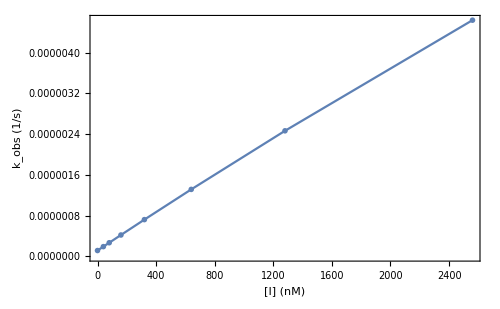

```mathematica
ListLinePlot[kobsItkExp,
ImageSize->500,LabelStyle->{14,Black},PlotMarkers->"OpenMarkers",
PlotRange->All,
Frame->True,FrameLabel->{"[I] (nM)", "k_obs (1/s)"},RotateLabel->False
]
```

```mathematica
u2ATP=1+100/KmATPitk
```

34/9

```mathematica
kobsLmItkExp=LinearModelFit[kobsItkExp[[;;]],x,x]
```

FittedModel[1.41975×10^-7+1.77013×10^-9 x]

```mathematica
kobsLmItkExp["ParameterTableEntries"][[2,1]]*u2ATP
```

6.68715×10^-9

```mathematica
ttblitk={10,100,1000,2000,4000,10000,14000,20000,30000,40000,100000,200000,300000}
```

{10,100,1000,2000,4000,10000,14000,20000,30000,40000,100000,200000,300000}

```mathematica
ttblitkEVB={10,100,1000,2000,4000,10000,14000,30000,40000,50000,200000,300000,500000, 600000, 800000, 1000000,1200000,1500000,1800000, 2000000,2300000,2500000,2800000,3000000,3300000,3500000,3700000,4000000}
```

{10,100,1000,2000,4000,10000,14000,30000,40000,50000,200000,300000,500000,600000,800000,1000000,1200000,1500000,1800000,2000000,2300000,2500000,2800000,3000000,3300000,3500000,3700000,4000000}

```mathematica
ic50tblExpItk=Transpose@{N@i0tblitk[[2;;]],#}&/@Table[yEI2[t]/yE[0]/.s[[1]],{t,ttblitk},{s,solExpItk[[2;;]]}];
```

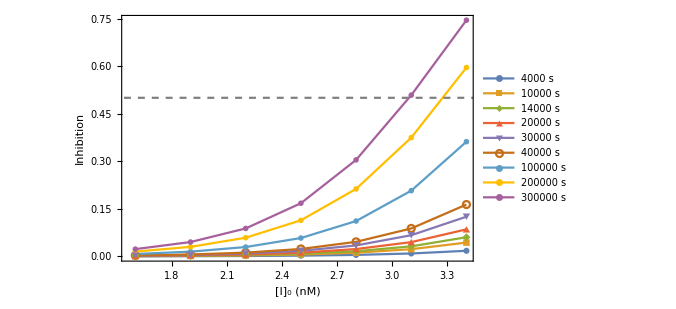

```mathematica
Show[ListLinePlot[ic50tblExpItk[[5;;]],PlotMarkers->Automatic,PlotRange->All,
Frame->True,FrameLabel->{"[I]_0 (nM)", "Inhibition"},
ImageSize->500,LabelStyle->{14,Black},
ScalingFunctions->{"Log10",None},PlotLegends->(ToString[NumberForm[#]]<>" s"&)/@ttblitk[[5;;]]],
Plot[0.5,{x,0.1,10000},ScalingFunctions->{"Log10",None},PlotStyle->{{Gray,Dashed}}]
]
```

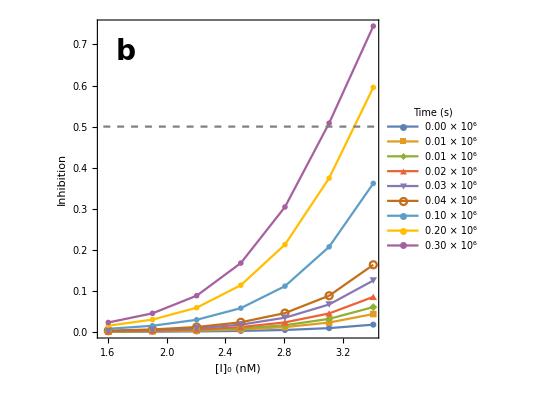

```mathematica
ic50ITKplt=Show[ListLinePlot[ic50tblExpItk[[5;;]],PlotMarkers->Automatic,PlotRange->All,
Frame->True,FrameLabel->{"[I]_0 (nM)", "Inhibition"},
ImageSize->400,AspectRatio->1,LabelStyle->{16,Black},
ScalingFunctions->{"Log10",None},
Epilog->{Inset[Style["b",28,Bold],Scaled@{0.1,0.9}]},PlotLegends->Placed[LineLegend[(ToString[NumberForm[#/1000000//N,{3,2}]]<>" × 10^6"&)/@ttblitk[[5;;]],LegendLabel->"Time (s)"],Right]],
Plot[0.5,{x,10,50000},ScalingFunctions->{"Log10",None},PlotStyle->{{Gray,Dashed}}]
]
```

```mathematica
Export["ic50_itk_assay.pdf",ic50ITKplt]
```

ic50_itk_assay.pdf

## ITK (Liclican)

## ITK EVB

```mathematica
karr={{0.0001094066673085099,0.000020440146958913697},{4.16291933639197*^9,3.926465819086454*^7},{0.004610330793167137,1.2699167034865527*^-23}}
```

{{0.000109407,0.0000204401},{4.16292×10^9,3.92647×10^7},{0.00461033,1.26992×10^-23}}

```mathematica
k1ITKrev=dGBarToRate[12] (* 1/s, 12 kcal/mol dissociation barrier*)
```

11303.2

```mathematica
KiITK=Exp[-10.23/kt]*10^(9) (* nM, PDLD 4.39 kcal/mol binding energy*)
```

35.2236

```mathematica
KiITK=Exp[-4.39/kt]*10^(9) (* nM, PDLD 4.39 kcal/mol binding energy*)
k1=k1ITKrev/KiITK(* 1 / (s nM) *)
```

633319.

0.0178476

```mathematica
(* Assume PT2 step is in equilibrium due to small barrier*)
```

```mathematica
jk1=(karr[[1,2]]*karr[[2,2]])/(karr[[2,1]]+karr[[2,2]])
jk2=(karr[[3,1]]*karr[[2,1]])/(karr[[2,1]]+karr[[2,2]])
```

1.9099×10^-7

0.00456725

```mathematica
(*kArr2={{karr[[1,1]], jk1},{jk2, karr[[3,2]]}}*)
```

```mathematica
kArr2={{karr[[1,1]], karr[[1,2]]},{karr[[3,1]], karr[[3,2]]}}
```

{{0.000109407,0.0000204401},{0.00461033,1.26992×10^-23}}

```mathematica
sol4hcv=Table[NDSolve[
Join[
EnzymeInhibitor3ODE[k1ATPitk, k1revATPitk, k1,k1ITKrev,kArr2[[1,1]],kArr2[[1,2]],kArr2[[2,1]], ksATPitk],
{yE[0]==5,yI[0]==i0,yS[0]==100000,
yP[0]==0,yEI1[0]==0,yEI2[0]==0,yEI3[0]==0,yES[0]==0}
],{yE,yI, yS,yP,yEI1,yEI2,yEI3,yES},{t,0,300000}
],{i0,i0tblitk}];
```

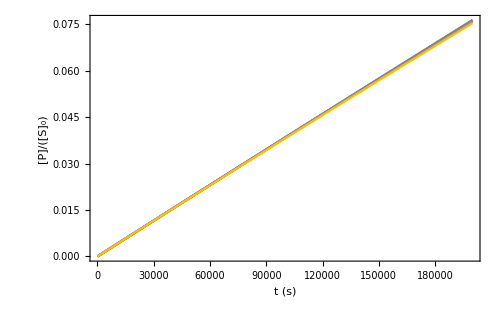

```mathematica
lt4hcvEVB=Plot[Evaluate@Table[yP[t]/yS[0]/.s,{s,sol4hcv}],{t,0,200000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},
Frame->True,FrameLabel->{"t (s)", "[P]/([S]_0)"},RotateLabel->False
]
```

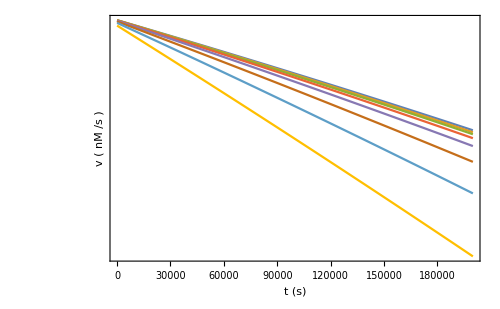

```mathematica
Plot[Evaluate@Table[yP'[t]/.s,{s,sol4hcv}],{t,0,200000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},ScalingFunctions->{None,"Log"},
Frame->True,FrameLabel->{"t (s)", "v ( nM /s )"},RotateLabel->False
]
```

```mathematica
(*Plot[Evaluate@Table[yEI3[t]/yE[0]/.s,{s,sol4hcv}],{t,0,200000},PlotRange->All,
ImageSize->500,LabelStyle->{14,Black},
Frame->True,FrameLabel->{"t (s)","[EI]/[E]_0"},RotateLabel->False
]*)
```

```mathematica
kobsItkEvb=Transpose@{i0tblitk,Table[-(Log[yP'[200000]]-Log[yP'[199000]])/1000/.s[[1]],{s,sol4hcv}]};
```

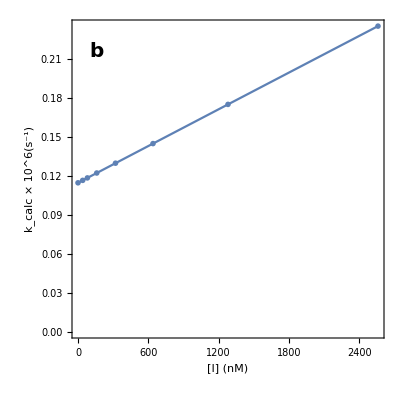

```mathematica
kobsplt4hcv= ListLinePlot[{#1,#2*1000000}&@@@kobsItkEvb,
ImageSize->400,LabelStyle->{16,Black},PlotMarkers->"OpenMarkers",
PlotRange->All,AspectRatio->1,
Frame->True,FrameStyle->Directive[Black],
Epilog->{Inset[Style["b",20,Bold],Scaled@{0.08,0.9}]},
FrameLabel->{"[I] (nM)", "k_calc × 10^6(s^-1)"},RotateLabel->False
]
```

```mathematica
Export["kcalc_4hcv.pdf",kobsplt4hcv]
```

kcalc_4hcv.pdf

```mathematica
kobsLm4hcv=LinearModelFit[kobsItkEvb,x,x]
```

FittedModel[1.14694×10^-7+4.70889×10^-11 x]

```mathematica
u2ATP=1+100/KmATPitk
```

34/9

```mathematica
kobsLm4hcv["ParameterTableEntries"][[2,1]]*u2ATP
```

1.77891×10^-10

```mathematica
ic50tbl4hcv=Transpose@{N@i0tblitk[[2;;]],#}&/@Table[yEI3[t]/yE[0]/.s[[1]],{t,ttblitkEVB},{s,sol4hcv[[2;;]]}];
```

InterpolatingFunction::dmval: Input value {500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

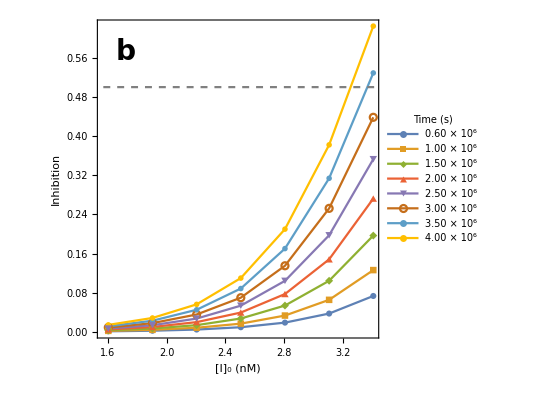

```mathematica
ic504hcvplt=Show[ListLinePlot[ic50tbl4hcv[[14;;;;2]],PlotMarkers->Automatic,PlotRange->All,
Frame->True,FrameLabel->{"[I]_0 (nM)", "Inhibition"},
ImageSize->400,AspectRatio->1,LabelStyle->{16,Black},
ScalingFunctions->{"Log10",None},
Epilog->{Inset[Style["b",28,Bold],Scaled@{0.1,0.9}]},PlotLegends->Placed[LineLegend[(ToString[NumberForm[#/1000000//N,{3,2}]]<>" × 10^6"&)/@ttblitkEVB[[14;;;;2]],LegendLabel->"Time (s)"],Right]],
Plot[0.5,{x,10,50000},ScalingFunctions->{"Log10",None},PlotStyle->{{Gray,Dashed}}]
]
```

```mathematica
Export["ic50_4hcv.pdf",ic504hcvplt]
```

ic50_4hcv.pdf

## ITK EVB